### Compute curvature of smooth curve using Mathematica

```mathematica
curvature[r0_] := Module[{r=r0},v=D[r,t]; T= v/(√(v.v));
κ=Simplify[√((1/(√(v.v))*D[T,t]).(1/(√(v.v))*D[T,t]))]]
```

```mathematica
r = {Cos[t],Sin[t]};
```

```mathematica
curvature[r]
```

1

```mathematica
r = {2Cos[t],2Sin[t]}
curvature[r]
```

{2 Cos[t],2 Sin[t]}

1/2

```mathematica
r = {Cos[t],Sin[t],t};
```

```mathematica
ParametricPlot3D[r,{t,0,2Pi}]
```

-Graphics3D-

```mathematica
r = {t-Cos[t],1-Sin[t]}
```

{t-Cos[t],1-Sin[t]}

```mathematica
curvature[r]
```

1/2 √(1/(2+2 Sin[t]))

```mathematica
f[t_] := 1/2 √(1/(2+2 Sin[t]))
```

```mathematica
f[0]
```

1/(2 √2)

```mathematica
f[Pi/4]
```

1/(2 √(2+√2))

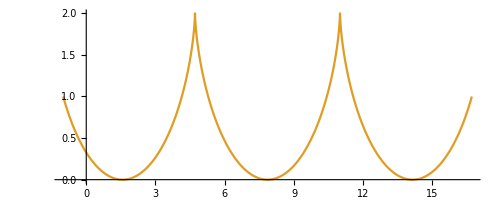

```mathematica
ParametricPlot[r,{t,0,5Pi}]
```